# Preconditioner for overparameterized problem

## Regular SGD on original and overparameterized

```mathematica
(* Batch dimension is last one *)
dsize=1000;
SeedRandom[0];
X=RandomVariate[normal,{dsize}]//Transpose;
wt = {1,1}; (* true w *)
w0={2,1}; (* initial w *)
Y=Dot[wt, X];
XY = X~Join~{Y};
grad[w_]:=2(w.X-Y).Transpose[X]/dsize;
loss[w_]:=Module[{error},
error=(w.X-Y);
Norm[error]^2/dsize
];
Print[loss[w0], " ",grad[w0]]
```

1.04094 {2.08189,2.06245}

```mathematica
(* takes loss, grad, learning rate, produces list of losses *)
optimize[loss_,grad_,w0_,pre_,lr_]:=Module[{gradstep},
gradstep[w_]:=w-lr*pre.grad[w];
points=NestList[gradstep,w0,100];
loss/@points
];
```

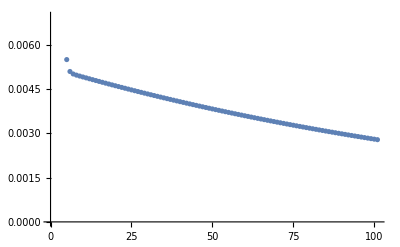

```mathematica
losses0=optimize[loss,grad,w0,IdentityMatrix[2],.15];
ListPlot@losses0
```

```mathematica
(* Augment with third component being sum of first two *)
Xa= X~Join~{{1,1}.X };
wat={1,1, 0}; 
wa0={2, 1, 0};
Ya=Dot[wat, Xa];
XYa = Xa~Join~{Ya};

lossa[wa_]:=Module[{error},
error=(wa.Xa-Ya);
Norm[error]^2/dsize
];
grada[w_]:=2(w.Xa-Y).Transpose[Xa]/dsize; (* grad for augmented problem *)
Print[lossa[wa0], " ",grada[wa0]]
```

1.04094 {2.08189,2.06245,4.14434}

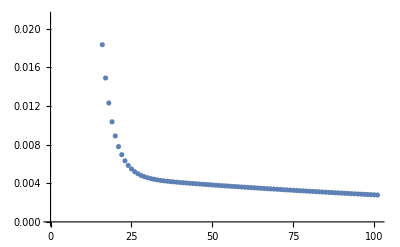

```mathematica
losses1=optimize[lossa,grada,wa0,IdentityMatrix[3],0.15];
ListPlot@losses1
```

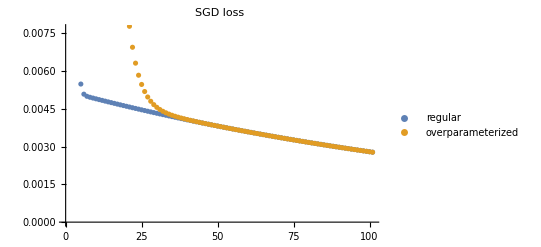

```mathematica
ListPlot[{losses0,losses1},PlotLabel->"SGD loss",PlotLegends->{"regular","overparameterized"},Axes->{"steps","loss"}]
```

## Tune SGD step size

```mathematica
(* Give largest step size that will produce improvement in objective for SGD *)
largestStep[w_]:=Module[{ee,g},
ee=w-wt; (* how far off from optimum *)
g=2(w.X-Y).Xᵀ/dsize; (* gradient *)
(2Dot[ee,g])/Dot[g,g]
];

(* Give step size that will produce best improvement in parameter space for SGD *)
idealStep[w_]:=Module[{ee,g},
ee=w-wt; (* how far off from optimum *)
g=2(w.X-Y).Xᵀ/dsize; (* gradient *)
Dot[ee,g]/Dot[g,g]
]
```

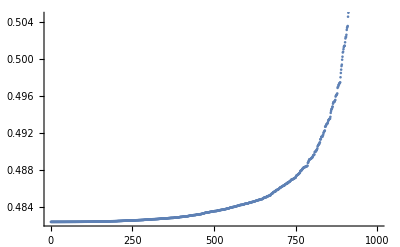

```mathematica
ListPlot[Sort[largestStep/@RandomReal[{-2,2},{1000,2}]]]
```

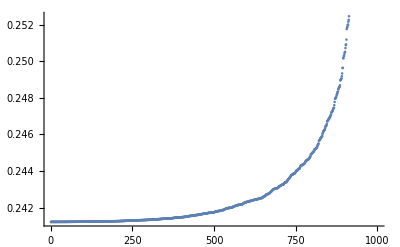

```mathematica
ListPlot[Sort[idealStep/@RandomReal[{-2,2},{1000,2}]]]
```

## Pseudo-inverse as preconditioner

```mathematica
cov=X.Xᵀ/dsize;
Eigenvalues[cov]
SingularValueDecomposition[cov][[2]]//Diagonal
```

{2.07282,0.0103625}

{2.07282,0.0103625}

```mathematica
cova=Xa.Xaᵀ/dsize;
Eigenvalues[cova]
SingularValueDecomposition[cova][[2]]//Diagonal
```

{6.21845,0.0103625,-6.41684×10^-16}

{6.21845,0.0103625,0.}

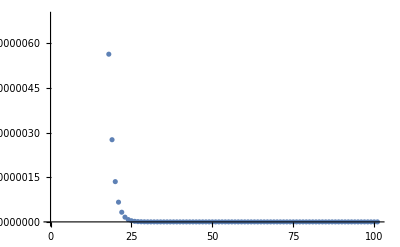

```mathematica
losses2=optimize[loss,grad,w0,Inverse@cov,0.15];
ListPlot@losses2
```

```mathematica
losses3=optimize[loss,grad,w0,PseudoInverse@cov,0.15];
ListPlot@losses3
```

-Graphics-

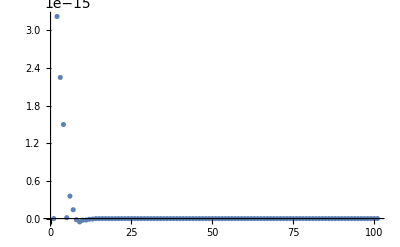

```mathematica
ListPlot[losses2-losses3]
```

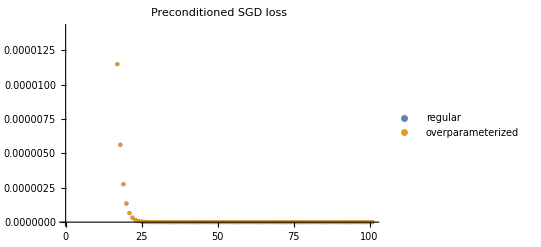

```mathematica
ListPlot[{losses2,losses3},PlotLabel->"Preconditioned SGD loss",PlotLegends->{"regular","overparameterized"},Axes->{"steps","loss"},PlotStyle->{PointSize[Medium],PointSize[Small]}]
```

## Generate data for TF test

```mathematica
Export["~/git/whitening/exp/linear-rankdeficient.csv",XYa]
```

~/git/whitening/exp/linear-rankdeficient.csv

```mathematica
losses1
```

{1.04094,0.781092,0.586415,0.440565,0.331294,0.249426,0.188086,0.142126,0.107688,0.0818805,0.0625395,0.0480428,0.0371751,0.0290263,0.0229143,0.0183282,0.0148854,0.012299,0.0103542,0.00889027,0.00778649,0.00695261,0.00632096,0.00584085,0.00547432,0.00519291,0.00497531,0.00480556,0.0046717,0.00456476,0.00447804,0.00440651,0.00434638,0.00429486,0.0042498,0.00420965,0.00417319,0.00413955,0.00410806,0.00407822,0.00404965,0.00402208,0.00399529,0.00396912,0.00394345,0.00391821,0.00389331,0.00386871,0.00384437,0.00382026,0.00379637,0.00377266,0.00374914,0.00372579,0.0037026,0.00367958,0.0036567,0.00363398,0.0036114,0.00358897,0.00356668,0.00354453,0.00352252,0.00350065,0.00347891,0.00345731,0.00343585,0.00341452,0.00339332,0.00337226,0.00335132,0.00333052,0.00330984,0.00328929,0.00326887,0.00324858,0.00322841,0.00320837,0.00318845,0.00316866,0.00314899,0.00312944,0.00311001,0.00309071,0.00307152,0.00305245,0.0030335,0.00301467,0.00299596,0.00297736,0.00295888,0.00294051,0.00292225,0.00290411,0.00288608,0.00286817,0.00285036,0.00283267,0.00281508,0.00279761,0.00278024}

```mathematica
Export["~/git/whitening/exp/linear-rankdeficient-losses.csv",losses1]
```

~/git/whitening/exp/linear-rankdeficient-losses.csv

```mathematica
Export["~/git/whitening/exp/linear-rankdeficient-losses-pre.csv",losses2]
```

~/git/whitening/exp/linear-rankdeficient-losses-pre.csv

```mathematica
losses2
```

{1.04094,0.510063,0.249931,0.122466,0.0600084,0.0294041,0.014408,0.00705992,0.00345936,0.00169509,0.000830593,0.000406991,0.000199425,0.0000977184,0.000047882,0.0000234622,0.0000114965,5.63327×10^-6,2.7603×10^-6,1.35255×10^-6,6.62749×10^-7,3.24747×10^-7,1.59126×10^-7,7.79717×10^-8,3.82062×10^-8,1.8721×10^-8,9.1733×10^-9,4.49492×10^-9,2.20251×10^-9,1.07923×10^-9,5.28822×10^-10,2.59123×10^-10,1.2697×10^-10,6.22154×10^-11,3.04856×10^-11,1.49379×10^-11,7.31958×10^-12,3.5866×10^-12,1.75743×10^-12,8.61142×10^-13,4.21959×10^-13,2.0676×10^-13,1.01312×10^-13,4.96431×10^-14,2.43251×10^-14,1.19193×10^-14,5.84046×10^-15,2.86183×10^-15,1.40229×10^-15,6.87124×10^-16,3.36691×10^-16,1.64979×10^-16,8.08395×10^-17,3.96113×10^-17,1.94096×10^-17,9.51069×10^-18,4.66024×10^-18,2.28352×10^-18,1.11892×10^-18,5.48272×10^-19,2.68653×10^-19,1.3164×10^-19,6.45036×10^-20,3.16068×10^-20,1.54873×10^-20,7.58879×10^-21,3.7185×10^-21,1.82206×10^-21,8.92808×10^-22,4.37478×10^-22,2.14363×10^-22,1.0504×10^-22,5.14692×10^-23,2.5221×10^-23,1.23588×10^-23,6.0563×10^-24,2.96751×10^-24,1.45419×10^-24,7.12519×10^-25,3.49072×10^-25,1.71126×10^-25,8.38211×10^-26,4.10211×10^-26,2.01102×10^-26,9.84532×10^-27,4.83882×10^-27,2.37231×10^-27,1.1544×10^-27,5.66026×10^-28,2.73774×10^-28,1.33736×10^-28,6.64473×10^-29,3.21606×10^-29,1.4829×10^-29,7.36327×10^-30,3.33633×10^-30,1.84869×10^-30,8.41922×10^-31,4.7223×10^-31,2.2797×10^-31,8.28012×10^-32}